### Plane Triangle Routines

```mathematica
phi=(1+Sqrt[5])/2
```

1/2 (1+√5)

```mathematica
Pts1={{0,1,phi},{0,1,-phi},{0,-1,phi},{0,-1,-phi}};
Pts2=Map[RotateLeft,Pts1];
Pts3=Map[RotateLeft,Pts2];
IPts=Join[Pts1,Pts2,Pts3];
IPts=Map[normalize,IPts]//Simplify;
PtPerm={7,5,1,9,3,6,8,4,12,2,11,10};
```

```mathematica
IPts=IPts[[PtPerm]];
```

```mathematica
(*??*)
```

```mathematica
normalize[x_]:=x/Norm[x]
```

```mathematica
trilabels={{1,2,3},{4,3,2},{3,4,5},{6,5,4},{5,6,7},{8,7,6},{7,8,9},{10,9,8},{9,10,1},{2,1,10},{2,11,4},{4,11,6},{6,11,8},{8,11,10},{10,11,2},{3,12,1},{5,12,3},{7,12,5},{9,12,7},{1,12,9}};
```

```mathematica
uplabels={{1,2,3},{3,4,5},{5,6,7},{7,8,9},{9,10,1},{2,11,4},{4,11,6},{6,11,8},{8,11,10},{10,11,2}};
downlabels={{4,3,2},{6,5,4},{8,7,6},{10,9,8},{2,1,10},{3,12,1},{5,12,3},{7,12,5},{9,12,7},{1,12,9}};
```

```mathematica
BC2SphereTri[alphaList_][trilab_]:=Map[normalize[#.IPts[[trilab]]]&,alphaList]
```

```mathematica
BC2Sphere[upalpha_,downalpha_]:=Module[{upPts,downPts},
upPts=Flatten[Map[BC2SphereTri[upalpha],uplabels],1];
downPts=Flatten[Map[BC2SphereTri[downalpha],downlabels],1];
{upPts,downPts}]
```

```mathematica
e[0]={1,0};
e[1]={1/2,Sqrt[3]/2};
```

```mathematica
Clear[x,y,ptri]
perp[{x_,y_}]={-y,x}
```

{-y,x}

```mathematica
func[{v0_,v1_,v2_}][x_]:=Module[{w},w=perp[v1-v0];
w.(x-v1)/(w.(v2-v1))]
```

```mathematica
PtinOpenTri[tri_][x_]:=(func[tri][x]>0&&func[RotateLeft[tri]][x]>0&&func[RotateLeft[tri,2]][x]>0)
```

```mathematica
PtinClosedTri[tri_][x_]:=(func[tri][x]>=0&&func[RotateLeft[tri]][x]>=0&&func[RotateLeft[tri,2]][x]>=0)
```

```mathematica
PlaneTri[j_]:=ptris[[j]]

SphereTri[j_]:=IPts[[trilabels[[j]]]]
```

```mathematica
TriLine[{a_,b_,c_}]:=Line[{a,b,c,a}]
```

```mathematica
Tri2a[ptri_][x_]:=Module[{a1,a2,a3},
{a2,a3}=Inverse[Transpose[{ptri[[2]]-ptri[[1]],ptri[[3]]-ptri[[1]]}]].(x-ptri[[1]]);
a1=1-a2-a3;
{a1,a2,a3}]
```

```mathematica
lattice[m_,n_]:=Module[{lattpts,ConvHullVerts,u0,u1,xmin,xmax,ymin,ymax},
u0=m*e[0]+n*e[1];
u1=(m+n)e[0]-m*e[1];
ConvHullVerts={{0,0},2u0,2u0+4u1,u0+5u1,-u0+5u1,-u0+u1};(*??*)
xmin=Min[ConvHullVerts[[All,1]]]-1;
xmax=Max[ConvHullVerts[[ All,1]]]+1;
ymin=Min[ConvHullVerts[[All,2]]]-1;
ymax=Max[ConvHullVerts[[ All,2]]]+1;
lattpts=Flatten[Table[i*e[0]+j*e[1],{j,-(5m+n+1),2n+1},{i,-1,6m+5n+1}],1];
Select[lattpts,((xmin<#[[1]]<xmax) && (ymin<#[[2]]<ymax))&]
]
```

```mathematica
IcoPlaneVerts[m_,n_]:=Module[{u,v,z1,z2},
u[0]=m*e[0]+n*e[1];
u[1]=RotationMatrix[-Pi/3].u[0];
u[2]=u[1]-u[0];
v={{0,0},u[0],u[1],u[0]+u[1],2u[1],u[0]+2u[1],3u[1],u[0]+3u[1],4u[1],u[0]+4u[1],5u[1],u[0]+5u[1]};
z1={2u[0],2u[0]+u[1],2u[0]+2u[1],2u[0]+3u[1],2u[0]+4u[1]};
z2={u[2],u[2]+u[1],u[2]+2u[1],u[2]+3u[1],u[2]+4u[1]};
Join[v,z1,z2]]

IcoPlaneTris[m_,n_]:=Module[{v,z1,z2},
v=IcoPlaneVerts[m,n];
z1=Take[v, {13,17}];
z2=Take[v, {18,22}];
 Join[Table[v[[{k,k+1,k+2}]],{k,1,10}],
Table[{v[[2k]],z1[[k]],v[[2k+2]]},{k,1,5}],Table[{v[[2k-1]],v[[2k+1]],z2[[k]]},{k,1,5}]]]
```

```mathematica
Clear[latt,ptris]
GetBC[m_,n_]:=Module[{ latt, ptris},
latt=lattice[m,n];
     ptris=IcoPlaneTris[m,n];
Map[Tri2a[ptris[[1]]],Select[latt,PtinOpenTri[ptris[[1]]]]]]

GetFullBC[m_,n_]:=Module[{ latt, ptris, bc},
latt=lattice[m,n];
     ptris=IcoPlaneTris[m,n];
bc=Map[Tri2a[ptris[[1]]],Select[latt,PtinClosedTri[ptris[[1]]]]];
Select[bc,(Not[MemberQ[#,1]]&&(#[[2]]≠0))&]]
```

```mathematica
GetFullBC[m_,n_]:=Module[{ latt, ptris, bc},
latt=lattice[m,n];
     ptris=IcoPlaneTris[m,n];
bc=Map[Tri2a[ptris[[1]]],Select[latt,PtinClosedTri[ptris[[1]]]]];
Select[bc,(Not[MemberQ[#,1]])&]]
```

```mathematica
UpDownBC[m_,n_]:=Module[{bc},
bc=GetFullBC[m,n];
{Select[bc,#[[1]]≠0&],Select[bc,(#[[2]]≠0 &&#[[3]]≠0)&]}]
```

```mathematica
SpherePts[PTS_,r_:.03]:=Map[Sphere[#,r]&,PTS]
```

```mathematica
PlotSpherePts[pts_,opt_:{}]:=Graphics3D[{RGBColor[0,1,1],Sphere[{0,0,0}], RGBColor[1,0,0],SpherePts[pts],opt}]
```

### Plot

```mathematica
t=lattice[3,2];
```

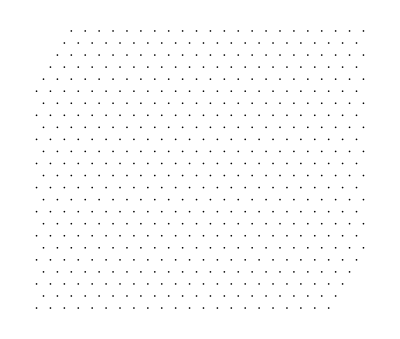

```mathematica
Show[Graphics[{PointSize[.003],Map[Point,t]}]]
```

```mathematica
latt=lattice[4,5];
ptris=IcoPlaneTris[4,5];
```

```mathematica
vlab={1,2,3,4,5,6,7,8,9,10,1,2};
```

```mathematica
vv=IcoPlaneVerts[4,5];
zz1=Take[vv, {13,17}];
zz2=Take[vv, {18,22}];
```

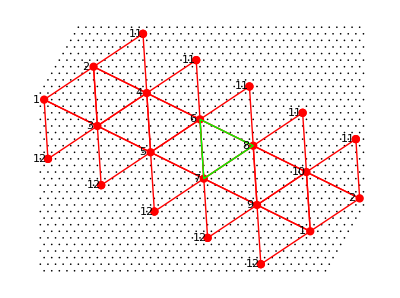

```mathematica
Show[Graphics[{PointSize[.003],Map[Point,latt],RGBColor[1,0,0],PointSize[.015],Map[Point,Join[vv,zz1,zz2]],Map[TriLine,ptris],RGBColor[0,1,0],TriLine[PlaneTri[6]],RGBColor[0,0,0],Table[Text[vlab[[k]],vv[[k]]-{1,0}],{k,1,Length[vlab]}],Table[Text[11,zz1[[k]]-{1,0}],{k,1,Length[zz1]}],Table[Text[12,zz2[[k]]-{1,0}],{k,1,Length[zz2]}]}]]
```

```mathematica
p=N[GetBC[2,3]]
```

{{0.368421,0.0526316,0.578947},{0.105263,0.157895,0.736842},{0.736842,0.105263,0.157895},{0.473684,0.210526,0.315789},{0.210526,0.315789,0.473684},{0.578947,0.368421,0.0526316},{0.315789,0.473684,0.210526},{0.0526316,0.578947,0.368421},{0.157895,0.736842,0.105263}}

```mathematica
{u,d}=BC2Sphere[p,p]
```

{{{0.,-0.108422,0.994105},{0.,-0.393374,0.919378},{0.,0.472163,0.881511},{0.,0.366005,0.930613},{0.,0.0879484,0.996125},{0.,0.902965,0.429714},{0.,0.989354,0.145528},{0.,0.717497,-0.696561},{0.,0.717497,-0.696561},{0.623495,0.555385,0.550274},{0.619792,0.78149,-0.0716317},{0.132813,-0.493438,0.859581},{0.566222,-0.310648,0.763472},{0.849333,0.430547,-0.305389},{0.0566814,-0.928552,0.366849},{0.377482,-0.804778,-0.458083},{0.396769,-0.0381897,-0.917124},{0.0885417,-0.609341,-0.787949},{-0.108422,0.994105,0.},{-0.393374,0.919378,0.},{0.472163,0.881511,0.},{0.366005,0.930613,0.},{0.0879484,0.996125,0.},{0.902965,0.429714,0.},{0.989354,0.145528,0.},{0.717497,-0.696561,0.},{0.717497,-0.696561,0.},{0.555385,0.550274,0.623495},{0.78149,-0.0716317,0.619792},{-0.493438,0.859581,0.132813},{-0.310648,0.763472,0.566222},{0.430547,-0.305389,0.849333},{-0.928552,0.366849,0.0566814},{-0.804778,-0.458083,0.377482},{-0.0381897,-0.917124,0.396769},{-0.609341,-0.787949,0.0885417},{0.327114,0.37064,0.869265},{-0.0521329,0.451079,0.89096},{0.677683,0.104708,0.727862},{0.325668,0.241529,0.914114},{-0.122771,0.341444,0.93185},{0.312932,0.0483506,0.948544},{-0.216949,0.178776,0.959673},{-0.553383,0.239407,0.797779},{-0.658621,0.0740091,0.748827},{0.0531687,-0.13144,-0.989897},{0.153338,-0.379074,-0.912574},{0.102226,0.347484,-0.932097},{0.221978,0.102892,-0.969608},{0.332967,-0.171487,-0.927214},{0.372181,0.328601,-0.868045},{0.499451,0.068595,-0.863623},{0.584856,-0.19716,-0.786811},{0.71558,0.0315895,-0.697817},{0.41463,-0.814877,-0.405041},{0.595591,-0.778758,-0.196994},{0.196994,-0.595591,-0.778758},{0.427763,-0.641644,-0.636641},{0.641644,-0.636641,-0.427763},{0.405041,-0.41463,-0.814877},{0.636641,-0.427763,-0.641644},{0.814877,-0.405041,-0.41463},{0.778758,-0.196994,-0.595591},{-0.0814655,-0.996089,-0.0342009},{-0.264431,-0.957994,-0.111014},{0.458685,-0.886259,-0.0644398},{0.359356,-0.920779,-0.151753},{0.210428,-0.940111,-0.268163},{0.718579,-0.654228,-0.235862},{0.666712,-0.651336,-0.362293},{0.570459,-0.625864,-0.531857},{0.825532,-0.282368,-0.488636},{-0.837752,-0.409337,0.361406},{-0.865352,-0.141443,0.480791},{-0.567251,-0.822744,0.0363203},{-0.63978,-0.761411,0.104573},{-0.778705,-0.569214,0.263845},{-0.0686145,-0.945371,-0.318694},{0.187993,-0.873168,-0.449706},{0.785249,-0.232187,-0.573998},{0.785249,-0.232187,-0.573998},{-0.515657,0.584271,-0.626678},{0.0587674,0.508484,-0.859064},{-0.928748,0.143499,0.341811},{-0.72764,0.539648,-0.423462},{0.169202,0.470578,-0.865983},{-0.928748,0.143499,0.341811},{0.426911,0.351794,-0.83306},{0.584768,0.252984,-0.770744},{0.777936,0.0874165,-0.622233}},{{0.,0.108422,-0.994105},{0.,0.393374,-0.919378},{0.,-0.472163,-0.881511},{0.,-0.366005,-0.930613},{0.,-0.0879484,-0.996125},{0.,-0.902965,-0.429714},{0.,-0.989354,-0.145528},{0.,-0.717497,0.696561},{0.,-0.717497,0.696561},{0.281159,-0.727787,-0.625521},{0.190147,-0.47088,-0.861462},{0.572138,-0.80158,-0.173576},{0.604957,-0.655689,-0.451773},{0.538161,-0.310192,-0.783686},{0.920417,-0.382082,-0.082737},{0.916924,0.0522098,-0.395631},{0.635497,0.486173,-0.599816},{0.725502,0.674221,-0.138104},{0.108422,-0.994105,0.},{0.393374,-0.919378,0.},{-0.472163,-0.881511,0.},{-0.366005,-0.930613,0.},{-0.0879484,-0.996125,0.},{-0.902965,-0.429714,0.},{-0.989354,-0.145528,0.},{-0.717497,0.696561,0.},{-0.717497,0.696561,0.},{-0.727787,-0.625521,0.281159},{-0.47088,-0.861462,0.190147},{-0.80158,-0.173576,0.572138},{-0.655689,-0.451773,0.604957},{-0.310192,-0.783686,0.538161},{-0.382082,-0.082737,0.920417},{0.0522098,-0.395631,0.916924},{0.486173,-0.599816,0.635497},{0.674221,-0.138104,0.725502},{-0.910107,0.409074,0.0660551},{-0.810021,0.178793,0.558479},{-0.207157,0.682826,-0.700596},{-0.593446,0.794668,-0.127769},{-0.67766,0.465352,0.569408},{-0.085688,0.953246,-0.289794},{-0.348305,0.807241,0.476493},{-0.398059,0.421738,0.814669},{-0.123066,0.646501,0.752922},{-0.0568655,0.140579,0.988435},{-0.184599,0.456354,0.870439},{-0.115717,-0.393345,0.91208},{-0.301182,-0.139606,0.943292},{-0.522457,0.26908,0.809095},{-0.579159,-0.511343,0.634904},{-0.890169,-0.122257,0.438922},{-0.942568,0.317749,0.102965},{-0.966731,-0.0426766,-0.252211},{0.305057,0.0184916,0.952155},{-0.126354,-0.476528,0.870032},{0.476528,0.870032,0.126354},{0.238555,0.808028,0.538685},{-0.538685,-0.238555,0.808028},{-0.0184916,0.952155,-0.305057},{-0.808028,0.538685,-0.238555},{-0.952155,-0.305057,0.0184916},{-0.870032,0.126354,-0.476528},{0.0814655,0.996089,-0.0342009},{0.264431,0.957994,-0.111014},{-0.458685,0.886259,-0.0644398},{-0.359356,0.920779,-0.151753},{-0.210428,0.940111,-0.268163},{-0.718579,0.654228,-0.235862},{-0.666712,0.651336,-0.362293},{-0.570459,0.625864,-0.531857},{-0.825532,0.282368,-0.488636},{-0.0686145,0.945371,0.318694},{-0.567251,0.822744,-0.0363203},{0.785249,0.232187,0.573998},{0.187993,0.873168,0.449706},{-0.63978,0.761411,-0.104573},{0.785249,0.232187,0.573998},{-0.778705,0.569214,-0.263845},{-0.837752,0.409337,-0.361406},{-0.865352,0.141443,-0.480791},{0.584768,0.252984,0.770744},{0.777936,0.0874165,0.622233},{0.0587674,0.508484,0.859064},{0.169202,0.470578,0.865983},{0.426911,0.351794,0.83306},{-0.515657,0.584271,0.626678},{-0.72764,0.539648,0.423462},{-0.928748,0.143499,-0.341811},{-0.928748,0.143499,-0.341811}}}

```mathematica
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[u,.015],RGBColor[1,1,0],SpherePts[d,.015]}]
```

-Graphics3D-